Separating Hyperplane example

```mathematica
Clear["Global`*"]
n=100;
d=3;
l1=RandomVariate[NormalDistribution[1,.4],{n,d}];
l2=RandomVariate[NormalDistribution[-1,.4],{n,d}];
x=Join[l1,l2];
y=Join[Table[1,{i,1,n}],Table[-1,{i,1,n}]];
SeparatingHyperplane[x_List,y_List]:=
Module[
{conditions,vars,b,w,ans,
dim=Length[x[[1]]] (* Dimension of training data*),
n=Length[x](* Size of training data *)},
vars=Table[w[i],{i,1,dim}];
conditions=Join[
{Norm[vars]^2} (* Cost function *),
Table[y[[i]](vars.x[[i]]+b)≥1,{i,1,n}] 
];
ans=Minimize[conditions,Join[vars,{b}]];
ans=#[[2]]&/@ans[[2]];
{ans[[1;;-2]],ans[[-1]]}
]
SeparatingHyperplane[x,y]
```

{{0.793423,0.394496,0.803202},-0.0269321}

```mathematica
w.#+b&/@l2
Flatten[Position[Ordering[%],1]]
Flatten[l2[[%]]]
s=Flatten[l1[[Flatten[Position[Ordering[w.#+b&/@l1],1]]]]]
Plot[Coefficient[f[t],t](X-s[[2]])+s[[1]],{X,-2,2}]
```

0.176482+1.35273 X+1.73778 Y

0.575447 (-0.176482-1.35273 X)

{Frame→True,FrameTicks→False,Axes→False,Ticks→False,PlotMarkers→{Automatic,Small}}

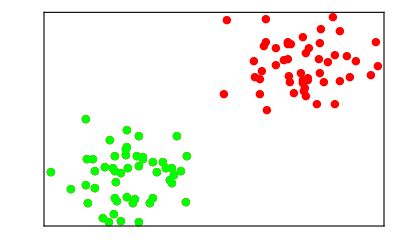

/Users/tdhopper/Dropbox/School/OR 706/Project/sep_plot_1.pdf

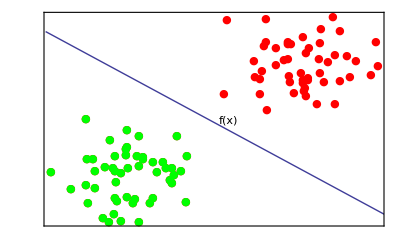

/Users/tdhopper/Dropbox/School/OR 706/Project/sep_plot_2.pdf

```mathematica
fcn=w.{X,Y}+b
f[X_]=Solve[fcn==0,Y][[1,1,2]]
sty={Frame->True,FrameTicks->False,Axes->False,Ticks->False,PlotMarkers->{Automatic,Small}}
Show[ListPlot[Join[l1,l2],PlotStyle->Red,sty],ListPlot[l2,PlotStyle->Green,sty]]
Export["/Users/tdhopper/Dropbox/School/OR 706/Project/sep_plot_1.pdf",%]
Show[ListPlot[Join[l1,l2],PlotStyle->Red,sty],ListPlot[l2,PlotStyle->Green,sty],
Plot[f[X],{X,-2,2},PlotStyle->sty],
Graphics[Text[Style["f(x)",Medium],{.15,-.05}]]
]
Export["/Users/tdhopper/Dropbox/School/OR 706/Project/sep_plot_2.pdf",%]
```

Other stuff

```mathematica
Clear["Global`*"]
n=10;
d=2;
l1=RandomVariate[NormalDistribution[3,1],{n,d}];
l2=RandomVariate[NormalDistribution[-3,1],{n,d}];
x=Join[l1,l2];
y=Join[Table[1,{i,1,n}],Table[-1,{i,1,n}]];
```

{Frame→True,FrameTicks→False,Axes→False,Ticks→False,PlotMarkers→{Automatic,Small}}

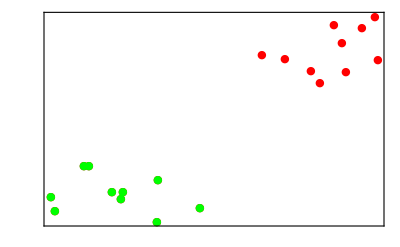

```mathematica
(*fcn=w.{X,Y}+b
f[X_]=Solve[fcn==0,Y][[1,1,2]]*)
sty={Frame->True,FrameTicks->False,Axes->False,Ticks->False,PlotMarkers->{Automatic,Small}}
Show[ListPlot[Join[l1,l2],PlotStyle->Red,sty],ListPlot[l2,PlotStyle->Green,sty]]
```

```mathematica
(*Primal SVN
*)SVN[x_List,y_List]:=Module[{conditions,vars,xi,b,w,d=Length[x[[1]]],n=Length[x],ans,C=10},
vars=Table[w[i],{i,1,d}];
xi=Table[ξ[i],{i,1,n}];
conditions=
Join[
{Total[#^2&/@vars]+C Sum[ξ[i],{i,1,n}]},Table[y[[i]](vars.x[[i]]+b)≥1-ξ[i],{i,1,n}],
Table[ξ[i]≥0,{i,1,n}]
];
ans=#[[2]]&/@NMinimize[conditions,Join[xi,vars,{b}]][[2]];
{ans[[-(Length[vars]+1);;-2]],ans[[-1]]}

]
(*Dual SVN by Default Minimization
*)SVN2[x_List,y_List]:=Module[{conditions,alpha,d=Length[x[[1]]],n=Length[x],ans,C=10},
alpha=Table[α[i],{i,1,n}];
conditions=
Join[
{∑_(i=1)^n α[i]-1/2∑_(i=1)^n ∑_(j=1)^n y[[i]]y[[j]]α[i]α[j](x[[i]].x[[j]])},
Table[0≤α[i]≤C,{i,1,n}],
{Sum[α[i]y[[i]],{i,1,n}]==0}
];
Print[conditions];
(*ans=#[[2]]&/@NMinimize[conditions,alpha][[2]];
{ans[[1;;-2]],ans[[-1]]}*)
Maximize[conditions,alpha]

]
```

```mathematica
ans=SVN2[x,y]
```

```mathematica
alpha=#[[2]]&/@ans[[2]]
```

{-7.54291×10^-13,0.00253627,0.,0.,0.,0.,0.,0.,0.,0.,3.52501×10^-9,1.267×10^-8,2.10966×10^-8,7.39163×10^-9,1.48413×10^-9,1.06595×10^-9,5.14138×10^-9,0.0025362,1.40341×10^-8,1.06993×10^-9}

```mathematica
w=∑_(i=1)^n alpha[[i]]y[[i]]x[[i]]
```

{0.00552013,0.00491768}

0.00552013 X+0.00491768 Y

-1.12251 X

{Frame→True,FrameTicks→False,Axes→False,Ticks→False,PlotMarkers→{Automatic,Small}}

-Graphics-

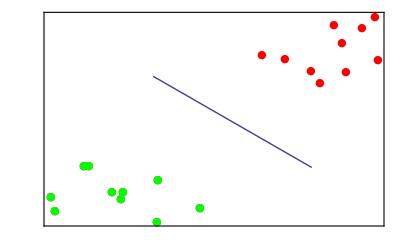

{{{0.290205,1.2116,-1.81732}},{{2.57274,0.14454,3.559}},{{0.170647,-0.314478,2.2933}},{{-0.5279,0.380968,-0.306646}},{{1.82183,2.2052,0.36458}},{{-0.538642,-0.289783,2.53607}},{{1.56155,-0.00142148,1.88392}},{{-0.960346,1.24448,-3.8128}},{{2.12545,0.180002,0.226409}},{{2.63535,1.38401,-0.307752}},{{0.0184687,1.42883,-1.70807}},{{2.64654,0.504245,0.84927}},{{2.32804,-1.69177,-0.481049}},{{3.65286,1.87015,1.67818}},{{0.787928,-1.47955,-1.93456}},{{3.15446,1.41296,-0.478384}},{{0.362822,-2.36938,-0.721613}},{{-0.431566,1.67929,1.76313}},{{1.31925,1.13601,2.2995}},{{3.75089,0.655409,-0.459156}},{{0.544914,-1.23058,-0.601554}},{{-0.755364,-2.74777,-2.02074}},{{-0.871088,3.67773,0.248505}},{{1.90163,-0.170364,1.4656}},{{2.19904,1.65928,0.682699}},{{-0.0043732,1.20246,-0.0475625}},{{0.861072,-0.852247,-0.434083}},{{-0.221021,0.227708,1.51119}},{{1.59894,2.23992,0.95671}},{{1.17624,-0.300734,0.31797}},{{1.37463,-1.55214,0.71777}},{{1.39217,2.81479,4.13511}},{{2.25217,0.26398,0.496388}},{{0.1287,-1.03781,-0.661503}},{{-2.3195,0.160399,0.731421}},{{1.81215,2.14248,0.553473}},{{1.16446,0.440894,2.07201}},{{-0.833503,1.00604,-1.25504}},{{0.0979102,0.604452,0.121672}},{{-0.285503,-1.05148,0.803046}},{{0.275249,0.278736,-0.460403}},{{0.678191,-3.28338,-0.0785721}},{{0.304754,1.4186,-0.501735}},{{1.30612,-2.37567,-2.14147}},{{3.00149,-0.263166,0.562701}},{{1.34105,0.285937,-1.14492}},{{3.84175,0.832572,2.21324}},{{-0.379826,-0.438689,-2.03701}},{{1.22228,0.436906,-1.77478}},{{-0.964616,1.8872,-0.539391}}}

```mathematica
fcn=w.{X,Y}+0
f[X_]=Solve[fcn==0,Y][[1,1,2]]
sty={Frame->True,FrameTicks->False,Axes->False,Ticks->False,PlotMarkers->{Automatic,Small}}
Show[ListPlot[Join[l1,l2],PlotStyle->Red,sty],ListPlot[l2,PlotStyle->Green,sty]]

Show[ListPlot[Join[l1,l2],PlotStyle->Red,sty],ListPlot[l2,PlotStyle->Green,sty],
Plot[f[X],{X,-2,2},PlotStyle->sty]]
```

SMO Algorithm

```mathematica
l1
```

{{2.84801,2.14633,-2.26551},{-0.287551,-2.73635,1.09133},{0.239288,1.61357,-2.22604},{4.06059,-0.870339,2.30275},{3.56052,0.883712,-2.27784},{1.12748,-0.445486,1.7398},{0.732883,0.792649,1.53191},{1.17703,2.63884,-1.32413},{3.9314,1.31448,-0.71697},{1.24249,0.564089,1.98119},{1.65672,-1.45,0.00289383},{3.59989,0.133636,0.927406},{2.87112,-0.849661,-1.38412},{2.93371,0.668802,1.63521},{2.88553,-1.36124,-0.369491},{3.86332,2.70519,-1.00774},{1.45809,-4.37609,1.12248},{1.86857,0.000432645,1.61206},{2.3772,1.21015,1.24495},{2.71527,-1.01377,1.39967},{1.65879,-1.20723,0.159021},{2.2217,-0.690494,2.01883},{2.60727,0.461291,0.402539},{0.278549,0.0901487,0.280332},{3.00001,0.12147,-1.15032},{-1.40809,0.435258,0.497491},{4.24715,2.54735,0.355375},{2.39376,0.208985,0.908268},{1.41454,1.72472,0.0716829},{2.16714,-0.1875,1.24618},{2.38054,0.157556,0.646039},{0.842561,-1.34964,2.32634},{2.41057,-2.63861,2.15427},{3.10689,0.0897303,0.225554},{2.59671,-0.868842,-1.9695},{1.23265,-0.879065,1.71236},{2.4255,-1.30366,0.58969},{2.07021,1.96284,1.21748},{2.17547,-1.6485,-1.24231},{-1.65708,0.283806,0.535095},{2.35041,-1.93758,-2.29724},{3.53982,-2.05107,0.392374},{2.77583,0.172407,-0.874561},{1.93861,0.138775,0.210647},{2.30228,-2.38476,1.65127},{1.17537,1.21617,2.00178},{0.865735,-1.3972,-0.25408},{2.3639,-0.572853,0.391951},{-0.416199,-1.51103,-0.583178},{2.19366,-0.295036,0.944416}}

```mathematica
ListPointPlot3D[#+{1,0,0}&/@RandomVariate[NormalDistribution[0,1],{10000/2,3}],AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
n=100;
d=3;
l1=RandomVariate[NormalDistribution[1,1.5],{n/2,d}];
l2=RandomVariate[NormalDistribution[-1,1.5],{n/2,d}];
l1=#+{2,0,0}&/@RandomVariate[NormalDistribution[0,1.5],{n/2,d}];
l2=#+{-2,0,0}&/@RandomVariate[NormalDistribution[0,1.5],{n/2,d}];
x=Join[l1,l2];
y=Join[Table[1,{i,1,n/2}],Table[-1,{i,1,n/2}]];
c=1;
tol=0.0001;
maxPasses=20;
b=0;
passes=0;
numChangedAlphas=0;
αn=Table[0,{i,1,n}];
f[X_,α_,b_,Ker_:Dot]:=Sum[α[[i]]y[[i]]Dot[x[[i]],X] ,{i,1,n}]+b
e[x_,y_,α_,i_,b_]:=f[x[[i]],α,b]-y[[i]]
η[x_,y_,i_,j_,Ker_:Dot]:=2(Dot[x[[i]],x[[j]]])-Dot[x[[i]],x[[i]]]-Dot[x[[j]],x[[j]]]
L[x_,y_,i_,j_,α_,c_:c]:=If[y[[i]]==y[[j]],Max[0,α[[j]]+α[[i]]-c],Max[0,α[[j]]+α[[i]]-c]];

H[x_,y_,i_,j_,α_,c_:c]:=If[y[[i]]==y[[j]],Min[c,α[[i]]+α[[j]]],Min[c,c+α[[j]]-α[[i]]]];
ActOnParameteri[x_,y_,α_,i_,b_,c_:c,tol_:tol]:=(y[[i]]e[x,y,α,i,b]<-tol&&α[[i]]<c)||(y[[i]]e[x,y,α,i,b]>tol&&α[[i]]>0)

PT[x_]:=If[False,Print[ToString[x]]]
iStep[x_,y_,α_,i_,b_]:=Module[{j,n=Length[x],c=c,αn=α,αiold,αjold,l,h,eta,tol=tol,b1,b2,Ker=Dot,bb=b},
j=RandomInteger[{1,n-1}];
If[j==i,j=n];
{αiold,αjold}={αn[[i]],αn[[j]]};
l=L[x,y,i,j,αn];
h=H[x,y,i,j,αn];
eta=η[x,y,i,j];
If[l==h,Return[{αn,bb}]];
If[eta≥0,Return[{αn,bb}]];
αn[[j]]=αn[[j]]-1/eta(y[[j]](e[x,y,αn,i,b]-e[x,y,αn,j,b]));
αn[[j]]=Piecewise[{{h,αn[[j]]>h},{l,αn[[j]]<l}},αn[[j]]];
If[Abs[αn[[j]]-αjold]<tol,Return[{αn,bb}]];
αn[[i]]=αn[[i]]+y[[i]]y[[j]](αjold-αn[[j]]);
b1=bb-e[x,y,αn,i,bb]-y[[i]](αn[[i]]-αiold)Dot[x[[i]],x[[i]]]-y[[j]](αn[[j]]-αjold)Dot[x[[i]],x[[j]]];
b2=bb-e[x,y,αn,j,bb]-y[[i]](αn[[i]]-αiold)Dot[x[[i]],x[[j]]]-y[[j]](αn[[j]]-αjold)Dot[x[[j]],x[[j]]];
bb=Piecewise[{{b1,0<αn[[i]]<c},{b2,0<αn[[j]]<c}},(b1+b2)/2];

numChangedAlphas++;
Return[{αn,bb}];
]
```

```mathematica
passes=0;
While[passes<maxPasses,
numChangedAlphas=0;
For[i=1,i≤n,i++,

If[ActOnParameteri[x,y,αn,i,b],{αn,b}=iStep[x,y,αn,i,b]];
]
If[numChangedAlphas==0,passes++,passes=0]
]
Beep[];Beep[]
```

```mathematica
Sign[f[#,αn,b]&/@x]-y//Tally
```

{{0,74},{-2,11},{2,15}}

```mathematica
f[{X,Y},αn,b]==0
F[X_]=Solve[%,Y][[1,1,2]]
sty={Frame->True,FrameTicks->False,Axes->False,Ticks->False,PlotMarkers->{Automatic,Small}};
Show[ListPlot[Join[l1,l2],PlotStyle->Red,sty],ListPlot[l2,PlotStyle->Green,sty]]
Show[ListPlot[Join[l1,l2],PlotStyle->Red,sty],ListPlot[l2,PlotStyle->Green,sty],
Plot[F[X],{X,-5,5},PlotStyle->sty]
]
```

```mathematica
f[{X,Y,Z},αn,b]==0;
F[X_,Y_]=Solve[%,Z][[1,1,2]];
sty3D={Frame->{False},AxesLabel->False,Axes->False,Ticks->{False,False,False}};
p1=ListPointPlot3D[{l1,l2},PlotStyle->{{Red,Green},PointSize->Medium}];
Show[p1]
Manipulate[Show[p1,
Plot3D[F[X,Y],{X,-u,u},{Y,-u,u}]
],{u,.1,10}]
```

-Graphics3D-